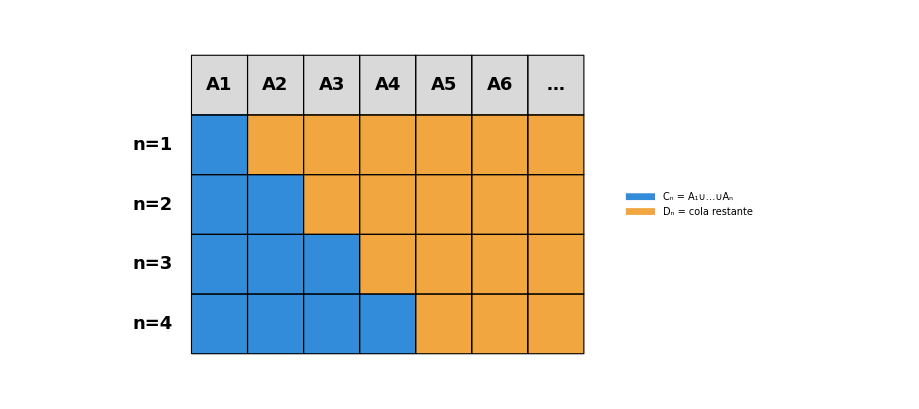

```mathematica
nBloques=6;  (*número de piezas A_i dibujadas explícitamente*)
nMax=4;      (*filas que ilustran n=1,...,nMax*)

colorC=RGBColor[0.2,0.55,0.85];   (*Cn=unión ya acumulada*)
colorD=RGBColor[0.95,0.65,0.25];  (*Dn=cola restante*)

totalCols=nBloques+1; (*bloques+columna final "..." para el resto infinito*)

filaCabecera=Table[{LightGray,EdgeForm[Black],Rectangle[{k-1,0},{k,1}],Black,Text[Style[If[k<=nBloques,"A"<>ToString[k],"…"],18,Bold],{k-0.5,0.5}]},{k,1,totalCols}];

filasDatos=Table[Table[{If[k<=n,colorC,colorD],EdgeForm[Black],Rectangle[{k-1,-n},{k,-n+1}]},{k,1,totalCols}],{n,1,nMax}];

etiquetasFila=Table[Text[Style["n="<>ToString[n],18,Bold],{-0.7,-n+0.5}],{n,1,nMax}];

grafico=Graphics[{filaCabecera,filasDatos,etiquetasFila},PlotRange->{{-2,totalCols+0.3},{-nMax-0.3,1.3}},ImageSize->680];

imagenFinal=Legended[grafico,SwatchLegend[{colorC,colorD},{"Cₙ = A₁∪…∪Aₙ","Dₙ = cola restante"},LabelStyle->Directive[FontSize->16],LegendMarkerSize->20]];

imagenFinal
```

```mathematica
Export["teorema4_continuidad_sigma_aditividad.png",imagenFinal,ImageResolution->600];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["teorema4_continuidad_sigma_aditividad.png"]]]
```